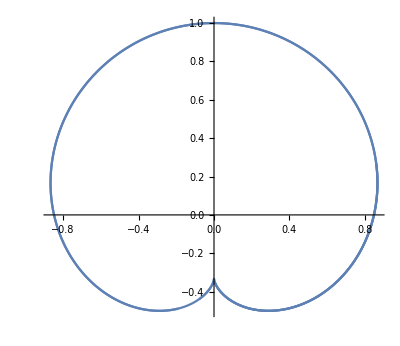

```mathematica
ClearAll["Global`*"]

F[x_,y_,t_]:=Sin[(2*Pi*t*4)/(2^Floor[Log[4*t]])-(2*Pi*t)/(2^Floor[Log[t]])]-y*(Sin[(2*Pi*t*4)/(2^Floor[Log[4*t]])]-Sin[(2*Pi*t)/(2^Floor[Log[t]])])-x*(Cos[(2*Pi*t*4)/(2^Floor[Log[4*t]])]-Cos[(2*Pi*t)/(2^Floor[Log[t]])]);
Fd[x_,y_,t_]:= 2*Pi*(
(4/(2^Floor[Log[4*t]]))*(Cos[(2*Pi*t)/(2^Floor[Log[t]])-(2*Pi*t*4)/(2^Floor[Log[4*t]])]-y*Cos[(2*Pi*t*4)/(2^Floor[Log[4*t]])]+x*Sin[(2*Pi*t*4)/(2^Floor[Log[4*t]])])
-(1/(2^Floor[Log[t]]))*(Cos[(2*Pi*t)/(2^Floor[Log[t]])-(2*Pi*t*4)/(2^Floor[Log[4*t]])]-y*Cos[(2*Pi*t)/(2^Floor[Log[t]])]+x*Sin[(2*Pi*t)/(2^Floor[Log[t]])])
);
parametricFunc[t_]:={x,y}/.(Solve[F[x,y,t]==0&&Fd[x,y,t]==0,{x,y}]);
ParametricPlot[parametricFunc[t],{t,0,2}]
```

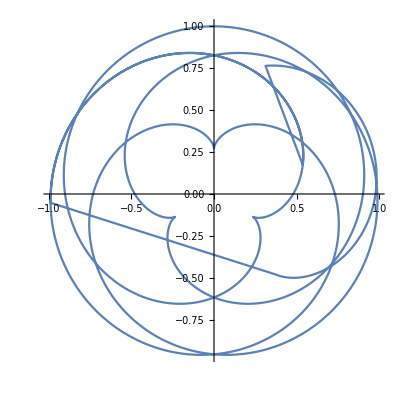

```mathematica
F[x_,y_,t_]:=(Cos[2^(1-Floor[Log[t]]) π t]-Cos[7 2^(1-Floor[Log[7 t]]) π t]) x+(Sin[2^(1-Floor[Log[t]]) π t]-Sin[7 2^(1-Floor[Log[7 t]]) π t])y-Sin[2 (2^(-Floor[Log[t]])-7 2^(-Floor[Log[7 t]])) π t];
Fd[x_,y_,t_]:= -2^(-Floor[Log[t]]) (Cos[2 (2^(-Floor[Log[t]])-7 2^(-Floor[Log[7 t]])) π t]-Cos[2^(1-Floor[Log[t]]) π t] y+x Sin[2^(1-Floor[Log[t]]) π t])+7 2^(-Floor[Log[7 t]]) (Cos[2 (2^(-Floor[Log[t]])-7 2^(-Floor[Log[7 t]])) π t]-Cos[7 2^(1-Floor[Log[7 t]]) π t] y+x Sin[7 2^(1-Floor[Log[7 t]]) π t]);
parametricFunc[t_]:={x,y}/.(Solve[F[x,y,t]==0&&Fd[x,y,t]==0,{x,y}]);
ParametricPlot[parametricFunc[t],{t,80,160}]
```